```mathematica
κ=7.5
```

7.5

```mathematica
p[n_,ρ_]:=n^3 - κ*n^2+(1+κ/ρ)*n-κ
```

```mathematica
R1[ρ_]:=NRoots[p[n,ρ],n][[1]][[2]]
R2[ρ_]:=NRoots[p[n,ρ],n][[2]][[2]]
R3[ρ_]:=NRoots[p[n,ρ],n][[3]][[2]]
```

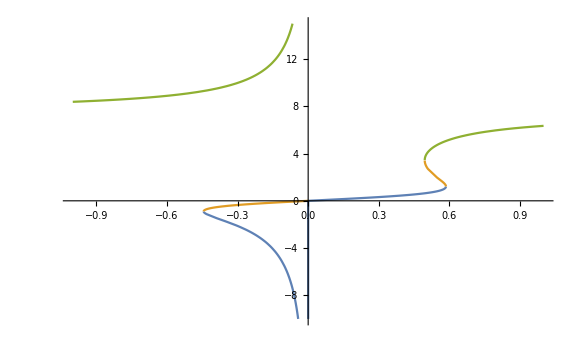

```mathematica
Plot[{R1[ρ],R2[ρ],R3[ρ]},{ρ,-1,1},PlotRange->{-10,15},ImageSize->Large]
```

```mathematica
DN[n_,ρ_]:=D[p[m,ρ],m] /. m -> n
```

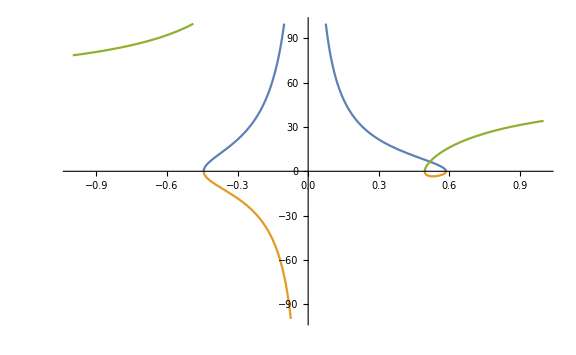
Zoom[-Graphics-]

```mathematica
Plot[{DN[R1[ρ],ρ],DN[R2[ρ],ρ],DN[R3[ρ],ρ]},{ρ,-1,1},PlotRange->{-100,100},ImageSize->Large]
```